```mathematica
g=9.8; (*grav. constant*)
l=0.5; (*length of pendulum*)

θ0=20*π/180; (*20 degrees*)
ω0 = 0; (*starting from rest*)
(*ϕ=y;
t=x;*)
ode1={θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0};
sol=NDSolve[ode1,θ,{t,0,20}];
```

```mathematica
myplot1 = Plot[(180/Pi) θ[t]/.sol,{t,0,20},PlotStyle-> RGBColor[0,0,1],PlotRange-> All];
omega=√(g/l);
```

```mathematica
approx = (180/Pi) θ0 Cos[omega*t];
myplot2=Plot[approx,{t,0,20},PlotStyle-> RGBColor[1,0,0],PlotRange-> All];
```

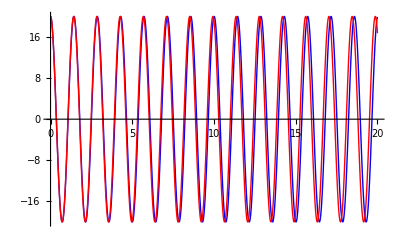

```mathematica
Show[{myplot1,myplot2}]
```

```mathematica
Manipulate[
g=9.8; l=0.5; omega=√(g/l);
Module[
{result = NDSolve[{θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0},θ, {t, 0,20}]},
Plot[{(180/Pi) θ0 Cos[omega*t],(180/Pi)* θ[t]/.result},{t,0,20},PlotStyle-> {{Blue},{Dashed,Red}},PlotRange-> All,AxesLabel->{"t (s)","θ (rad)"},PlotRange->{{0,20},{-20,20}},ImageSize->{500,300}]],
{{l,0.5,"length (m)"},0,2,Appearance->"Labeled"},{{θ0,20*Pi/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{ω0,0,"initial speed (rad/s)"},0,10.,Appearance->"Labeled"}]
```

```mathematica
ode=x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]
ode2 = y''[t]==-g (1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2])
```

x''[t]==-0.00098 x'[t] √(x'[t]^2+y'[t]^2)

y''[t]==-9.8 (1+(y'[t] √(x'[t]^2+y'[t]^2))/10000)

```mathematica
g=9.8;
x0=0;
y0=2;
V=30;
vt=100;(*This is a nonsense number*)
th=50 Pi/180;
x1=V Cos[th];
y1=V Sin[th];
sol=NDSolve[{ode,ode2, x[0]==x0,x'[0]==x1,y[0]==y0,y'[0]==y1},{x,y},{t,0,200}]
```

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>]}}

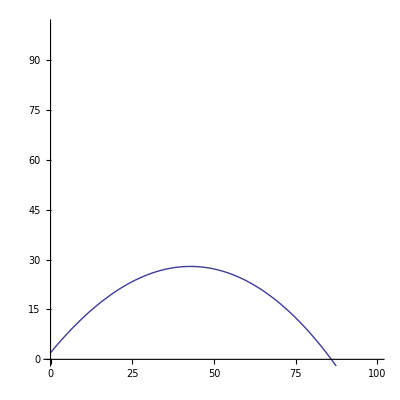

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,200},PlotRange->{{0,100},{0,100}}]
```

```mathematica
th=.;
vt=.;
V=.;
```

```mathematica
Manipulate[
g=9.8;x0=0;y0=1.5;
Module[
{result = NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2],y''[t]==-g (1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]), x[0]==x0,x'[0]==V Cos[th],y[0]==y0,y'[0]==V Sin[th]},{x,y},{t,0,tf}]},
ParametricPlot[{Evaluate[{x[t],y[t]}/.result],{x0+V t Cos[th],y0+V  Sin[th t]-0.5 g t^2}},{t,0,tf},PlotStyle-> {{Blue},{Red}},AxesLabel->{"distance (m)","height (m)"},PlotRange->{{0,100},{0,50}},ImageSize->{500,300}]],
{{V,38,"initial velocity (m/s)"},0,100,Appearance->"Labeled"},{{th,20 Pi/180,"angle (rad)"},.1,Pi/2,Appearance->"Labeled"},
{{vt,35,"terminal velocity (m/s)"},0,100,Appearance->"Labeled"},{{tf,3,"time (s)"},0.1,100,Appearance->"Labeled"}]
```

```mathematica
(*Human Cannonball*)
hcwithres={0.5354radians,31.8m/s}
hcnores={0.6677radians,36.8 m/s}
```

{0.5354 radians,(31.8 m)/s}

{0.6677 radians,(36.8 m)/s}

```mathematica
(*golfball*)
y0=0;
gbwithres={0.41475 radians,38m/s}
gbnores={0.41475 radians, 35.2m/s}
```

{0.41475 radians,(38 m)/s}

{0.41475 radians,(35.2 m)/s}

```mathematica
(*baseball*)
y0=1.5;
bbwithres={0.5206radians,35.5m/s}
bbnores={0.41475 radians,35.3m/s}
```

{0.5206 radians,(35.5 m)/s}

{0.41475 radians,(35.3 m)/s}

```mathematica
(*Civil War era cannonball*)
Manipulate[
g=9.8;x0=0;y0=1;
Module[
{result = NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2],y''[t]==-g (1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]), x[0]==x0,x'[0]==V Cos[th],y[0]==y0,y'[0]==V Sin[th]},{x,y},{t,0,tf}]},
ParametricPlot[{Evaluate[{x[t],y[t]}/.result],{x0+V t Cos[th],y0+V  Sin[th t]-0.5 g t^2}},{t,0,tf},PlotStyle-> {{Blue},{Red}},AxesLabel->{"distance (m)","height (m)"},PlotRange->{{0,6000},{0,500}},ImageSize->{700,300}]],
{{V,439,"initial velocity (m/s)"},0,500,Appearance->"Labeled"},{{th,5 Pi/180,"angle (rad)"},0,Pi/2,Appearance->"Labeled"},
{{vt,135,"terminal velocity (m/s)"},0,150,Appearance->"Labeled"},{{tf,10,"time (s)"},0.1,100,Appearance->"Labeled"}]
```

```mathematica
(*5degrees*)
dist=1650m
```

1650 m

```mathematica
(*10degrees*)
dist=2320m
```

2320 m

```mathematica
(*15degrees*)
dist=2720m
```

2720 m

```mathematica
(*to stay within 1000m*)
(*15degrees*)
v0=173m/s
```

(173 m)/s

```mathematica
(*10degrees*)
v0=209m/s
```

(209 m)/s

```mathematica
(*5degrees*)
v0=295m/s
```

(295 m)/s